6)
x = 2α*Cot [θ];
y = 2 α*Sin^2[θ];
α=3;

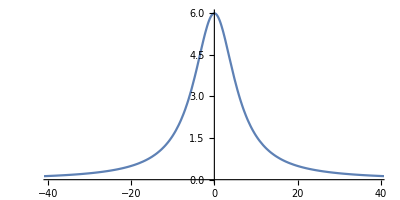

```mathematica
ClearAll["Global`*"]
x = 2α*Cot [θ];
y = 2 α*(Sin^2)[θ];
ParametricPlot[{6 Cot[u],6 Sin[u]^2},{u,0,2 Pi},AspectRatio->1/2]
```

```mathematica
D[6Cot [θ],θ]
```

-6 Csc[θ]^2

```mathematica
D[6 Sin[θ]^2,θ]
```

12 Cos[θ] Sin[θ]

```mathematica
Sqrt[(-6 Csc[θ]^2)^2 +(12 Cos[θ] Sin[θ])^2]
```

√(36 Csc[θ]^4+144 Cos[θ]^2 Sin[θ]^2)

```mathematica
∫_(π/4)^(π/2) √((-6 Csc[θ]^2)^2+(12 Cos[θ]Sin[θ])^2)ⅆθ
```

∫_(π/4)^(π/2) √(36 Csc[θ]^4+144 Cos[θ]^2 Sin[θ]^2)ⅆθ

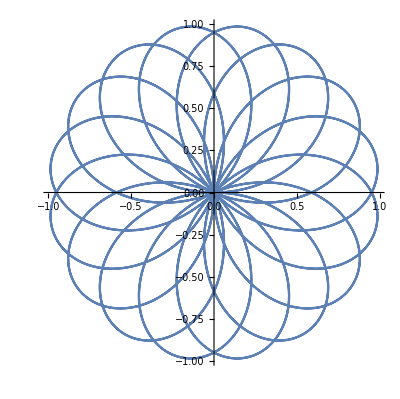

```mathematica
PolarPlot[Sin[(8θ)/5],{θ,0,20π}]
```